```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jinyunlin/QFE-Research/QFEgeometry/Mathematica

```mathematica
q3 = Import[ "/Users/jinyunlin/QFE-Research/QFEgeometry/data/q3_summary.txt","Table"];
q4 = Import[ "/Users/jinyunlin/QFE-Research/QFEgeometry/data/q4_summary.txt","Table"];
q5 = Import[ "/Users/jinyunlin/QFE-Research/QFEgeometry/data/q5_summary.txt","Table"];
```

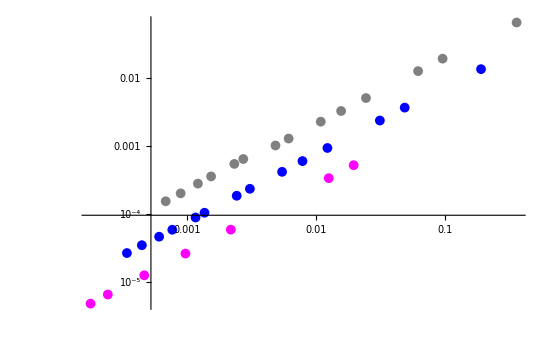

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-5}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-5}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-5}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```

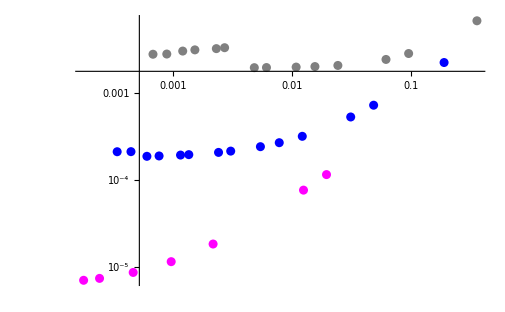

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-4}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-4}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-4}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```

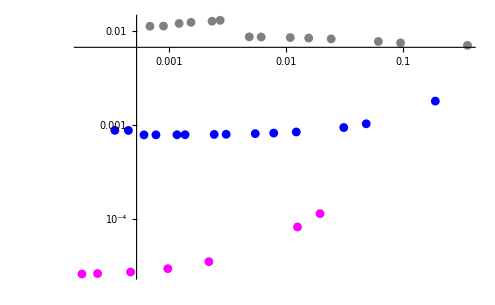

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-3}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-3}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-3}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```

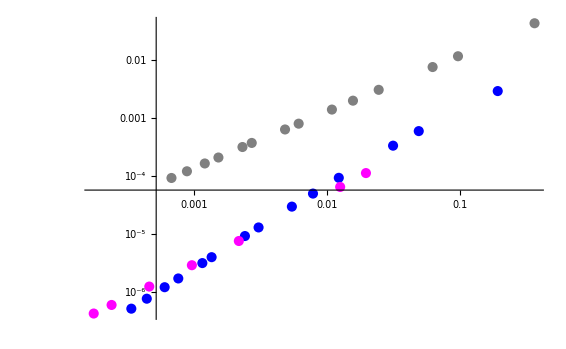

```mathematica
f1 = ListLogLogPlot[q3[[All, {2,-2}]], PlotStyle->Gray];
f2= ListLogLogPlot[q4[[All, {2,-2}]],PlotStyle->Blue];
f3 = ListLogLogPlot[q5[[All, {2,-2}]], PlotStyle->Magenta];
Show[f1,f2,f3, PlotRange->{All, All}]
```

```mathematica
data = Import["res10.txt", "table"];
```

```mathematica
test=Flatten[data[[All, {4}]]];
```

```mathematica
test
```

{5.8331×10^-8,-9.5877×10^-8,-7.8256×10^-7,-2.29766×10^-6,-4.77851×10^-6,-8.19679×10^-6,-0.0000123558,-0.0000168914,4.16276×10^-7,1.09094×10^-6,1.70766×10^-7,1.30257×10^-6,2.4727×10^-8,7.40437×10^-7,-8.49075×10^-7,-7.77429×10^-7,-2.75794×10^-6,-3.2431×10^-6,-5.8066×10^-6,-6.43611×10^-6,-9.88443×10^-6,-0.0000146693,1.20945×10^-6,3.27565×10^-6,9.71232×10^-7,4.96772×10^-6,2.03955×10^-6,5.85113×10^-6,2.45629×10^-6,5.66428×10^-6,1.87348×10^-6,4.37524×10^-6,1.31844×10^-7,-2.69541×10^-6,2.52387×10^-6,6.4105×10^-6,2.47204×10^-6,9.92881×10^-6,5.39168×10^-6,0.000012464,7.69354×10^-6,0.0000136311,8.90229×10^-6,8.77079×10^-6,4.345×10^-6,0.0000102953,4.71319×10^-6,0.0000157142,9.91178×10^-6,0.0000197649,0.0000144004,0.0000175341,6.57991×10^-6,0.0000146002,7.60555×10^-6,0.0000216878,0.0000152602,0.0000219222,9.06585×10^-6,0.0000188987,0.0000109575,0.0000209559,0.0000115824,0.0000144875,-2.228×10^-8,-4.75531×10^-7,-1.6931×10^-6,-3.9439×10^-6,-7.29828×10^-6,-0.0000116458,-0.0000167022,-0.0000220219,3.53149×10^-7,-4.16703×10^-7,-6.5227×10^-8,-2.47062×10^-6,-9.5595×10^-7,-5.95289×10^-6,-2.99679×10^-6,-0.0000107758,-6.41769×10^-6,-0.0000166045,-0.0000111942,-0.0000228765,-0.0000170664,-0.0000235536,1.53004×10^-6,7.21897×10^-7,5.75528×10^-7,-1.8975×10^-6,-7.79037×10^-7,-6.31261×10^-6,-3.87361×10^-6,-0.0000122134,-8.7539×10^-6,-0.0000189837,-0.0000151787,-0.0000226218,3.8575×10^-6,3.22147×10^-6,2.37688×10^-6,2.85213×10^-7,8.75951×10^-7,-4.76083×10^-6,-2.93867×10^-6,-0.0000113403,-8.89851×10^-6,-0.0000165016,7.46387×10^-6,7.14029×10^-6,5.67085×10^-6,4.04761×10^-6,4.25233×10^-6,-1.4158×10^-6,-2.338×10^-9,-6.69743×10^-6,0.0000122634,0.0000122665,0.0000105071,9.02853×10^-6,9.29947×10^-6,4.77788×10^-6,0.0000179588,0.0000181162,0.0000166565,0.0000156469,0.0000240497,0.0000236231,-7.2101×10^-8,-1.98017×10^-7,-2.63832×10^-7,-1.39805×10^-7,2.67928×10^-7,9.99284×10^-7,2.03332×10^-6,3.28113×10^-6,-1.98017×10^-7,-1.34848×10^-6,-2.11079×10^-7,-2.8295×10^-6,-6.15536×10^-7,-4.41953×10^-6,-1.00305×10^-6,-5.88239×10^-6,-1.20841×10^-6,-7.01907×10^-6,-1.11181×10^-6,-7.70232×10^-6,-6.63186×10^-7,1.12389×10^-7,-2.63832×10^-7,-2.8295×10^-6,-6.15536×10^-7,-6.14043×10^-6,-2.52102×10^-6,-9.75254×10^-6,-4.85031×10^-6,-0.0000132126,-7.28369×10^-6,-0.0000161078,-9.5128×10^-6,-0.0000112856,-1.39805×10^-7,-4.41953×10^-6,-1.00305×10^-6,-9.75254×10^-6,-4.85031×10^-6,-0.0000154064,-9.50974×10^-6,-0.0000206399,-0.0000144019,-0.0000189693,2.67928×10^-7,-5.88239×10^-6,-1.20841×10^-6,-0.0000132126,-7.28369×10^-6,-0.0000206399,-0.0000144019,-0.0000216733,9.99284×10^-7,-7.01907×10^-6,-1.11181×10^-6,-0.0000161078,-9.5128×10^-6,-0.0000189693,2.03332×10^-6,-7.70232×10^-6,-6.63186×10^-7,-0.0000112856,3.28113×10^-6,1.12389×10^-7,5.8331×10^-8,4.16276×10^-7,1.20945×10^-6,2.52387×10^-6,4.345×10^-6,6.57991×10^-6,9.06585×10^-6,0.0000115824,-9.5877×10^-8,1.09094×10^-6,1.70766×10^-7,3.27565×10^-6,9.71232×10^-7,6.4105×10^-6,2.47204×10^-6,0.0000102953,4.71319×10^-6,0.0000146002,7.60555×10^-6,0.0000188987,0.0000109575,0.0000144875,-7.8256×10^-7,1.30257×10^-6,2.4727×10^-8,4.96772×10^-6,2.03955×10^-6,9.92881×10^-6,5.39168×10^-6,0.0000157142,9.91178×10^-6,0.0000216878,0.0000152602,0.0000209559,-2.29766×10^-6,7.40437×10^-7,-8.49075×10^-7,5.85113×10^-6,2.45629×10^-6,0.000012464,7.69354×10^-6,0.0000197649,0.0000144004,0.0000219222,-4.77851×10^-6,-7.77429×10^-7,-2.75794×10^-6,5.66428×10^-6,1.87348×10^-6,0.0000136311,8.90229×10^-6,0.0000175341,-8.19679×10^-6,-3.2431×10^-6,-5.8066×10^-6,4.37524×10^-6,1.31844×10^-7,8.77079×10^-6,-0.0000123558,-6.43611×10^-6,-9.88443×10^-6,-2.69541×10^-6,-0.0000168914,-0.0000146693,-2.228×10^-8,-4.75531×10^-7,-1.6931×10^-6,-3.9439×10^-6,-7.29828×10^-6,-0.0000116458,-0.0000167022,-0.0000220219,3.53149×10^-7,-4.16703×10^-7,-6.5227×10^-8,-2.47062×10^-6,-9.5595×10^-7,-5.95289×10^-6,-2.99679×10^-6,-0.0000107758,-6.41769×10^-6,-0.0000166045,-0.0000111942,-0.0000228765,-0.0000170664,-0.0000235536,1.53004×10^-6,7.21897×10^-7,5.75528×10^-7,-1.8975×10^-6,-7.79037×10^-7,-6.31261×10^-6,-3.87361×10^-6,-0.0000122134,-8.7539×10^-6,-0.0000189837,-0.0000151787,-0.0000226218,3.8575×10^-6,3.22147×10^-6,2.37688×10^-6,2.85213×10^-7,8.75951×10^-7,-4.76083×10^-6,-2.93867×10^-6,-0.0000113403,-8.89851×10^-6,-0.0000165016,7.46387×10^-6,7.14029×10^-6,5.67085×10^-6,4.04761×10^-6,4.25233×10^-6,-1.4158×10^-6,-2.338×10^-9,-6.69743×10^-6,0.0000122634,0.0000122665,0.0000105071,9.02853×10^-6,9.29947×10^-6,4.77788×10^-6,0.0000179588,0.0000181162,0.0000166565,0.0000156469,0.0000240497,0.0000236231,-0.0000240497,-0.0000181162,-9.02853×10^-6,1.4158×10^-6,0.0000113403,0.0000189837,0.0000228765,0.0000220219,-0.0000179588,-0.0000122665,-0.0000236231,-4.04761×10^-6,-0.0000156469,4.76083×10^-6,-4.77788×10^-6,0.0000122134,6.69743×10^-6,0.0000166045,0.0000165016,0.0000167022,0.0000226218,0.0000235536,-0.0000122634,-7.14029×10^-6,-0.0000166565,-2.85213×10^-7,-9.29947×10^-6,6.31261×10^-6,2.338×10^-9,0.0000107758,8.89851×10^-6,0.0000116458,0.0000151787,0.0000170664,-7.46387×10^-6,-3.22147×10^-6,-0.0000105071,1.8975×10^-6,-4.25233×10^-6,5.95289×10^-6,2.93867×10^-6,7.29828×10^-6,8.7539×10^-6,0.0000111942,-3.8575×10^-6,-7.21897×10^-7,-5.67085×10^-6,2.47062×10^-6,-8.75951×10^-7,3.9439×10^-6,3.87361×10^-6,6.41769×10^-6,-1.53004×10^-6,4.16703×10^-7,-2.37688×10^-6,1.6931×10^-6,7.79037×10^-7,2.99679×10^-6,-3.53149×10^-7,4.75531×10^-7,-5.75528×10^-7,9.5595×10^-7,2.228×10^-8,6.5227×10^-8,-0.0000274586,-0.0000202949,-9.78539×10^-6,2.14424×10^-6,0.0000134819,0.0000223371,0.0000271301,0.0000267844,-0.000028304,-0.0000178608,-0.0000291255,-4.37416×10^-6,-0.000018587,9.69891×10^-6,-4.94334×10^-6,0.0000219014,9.27935×10^-6,0.0000300638,0.0000215737,0.0000325764,0.0000297146,0.0000320121,-0.0000261096,-0.0000126163,-0.0000280777,3.14856×10^-6,-0.0000137607,0.0000182156,2.81723×10^-6,0.0000297878,0.0000186109,0.0000356103,0.0000307571,0.0000368969,-0.0000212002,-5.27045×10^-6,-0.0000236149,0.0000116773,-6.16116×10^-6,0.0000262554,0.0000122114,0.0000355097,0.0000280332,0.0000382413,-0.0000142252,3.16219×10^-6,-0.0000163556,0.0000198809,3.15471×10^-6,0.0000322975,0.0000218004,0.0000358376,-6.07404×10^-6,0.0000114825,-7.28345×10^-6,0.0000263648,0.0000128359,0.000029972,2.20699×10^-6,0.0000184332,2.36265×10^-6,0.0000213834,9.5074×10^-6,0.0000112073,-0.0000307666,-0.0000333965,-0.0000328311,-0.0000292416,-0.0000231532,-0.0000153724,-6.91286×10^-6,1.09087×10^-6,-0.0000333965,-0.0000371581,-0.0000362676,-0.0000372846,-0.0000384219,-0.0000339544,-0.0000367109,-0.0000277841,-0.0000315226,-0.0000197449,-0.000023666,-0.0000110595,-0.0000142697,-4.67059×10^-6,-0.0000328311,-0.0000372846,-0.0000384219,-0.0000377887,-0.0000415379,-0.000034568,-0.0000403782,-0.0000283597,-0.0000353897,-0.0000203092,-0.0000275008,-0.0000180048,-0.0000292416,-0.0000339544,-0.0000367109,-0.000034568,-0.0000403782,-0.0000313863,-0.0000395168,-0.0000252836,-0.0000346714,-0.0000269084,-0.0000231532,-0.0000277841,-0.0000315226,-0.0000283597,-0.0000353897,-0.0000252836,-0.0000346714,-0.0000300286,-0.0000153724,-0.0000197449,-0.000023666,-0.0000203092,-0.0000275008,-0.0000269084,-6.91286×10^-6,-0.0000110595,-0.0000142697,-0.0000180048,1.09087×10^-6,-4.67059×10^-6,-0.0000274586,-0.000028304,-0.0000261096,-0.0000212002,-0.0000142252,-6.07404×10^-6,2.20699×10^-6,9.5074×10^-6,-0.0000202949,-0.0000178608,-0.0000291255,-0.0000126163,-0.0000280777,-5.27045×10^-6,-0.0000236149,3.16219×10^-6,-0.0000163556,0.0000114825,-7.28345×10^-6,0.0000184332,2.36265×10^-6,0.0000112073,-9.78539×10^-6,-4.37416×10^-6,-0.000018587,3.14856×10^-6,-0.0000137607,0.0000116773,-6.16116×10^-6,0.0000198809,3.15471×10^-6,0.0000263648,0.0000128359,0.0000213834,2.14424×10^-6,9.69891×10^-6,-4.94334×10^-6,0.0000182156,2.81723×10^-6,0.0000262554,0.0000122114,0.0000322975,0.0000218004,0.000029972,0.0000134819,0.0000219014,9.27935×10^-6,0.0000297878,0.0000186109,0.0000355097,0.0000280332,0.0000358376,0.0000223371,0.0000300638,0.0000215737,0.0000356103,0.0000307571,0.0000382413,0.0000271301,0.0000325764,0.0000297146,0.0000368969,0.0000267844,0.0000320121,-0.0000240497,-0.0000179588,-0.0000122634,-7.46387×10^-6,-3.8575×10^-6,-1.53004×10^-6,-3.53149×10^-7,2.228×10^-8,-0.0000181162,-0.0000122665,-0.0000236231,-7.14029×10^-6,-0.0000166565,-3.22147×10^-6,-0.0000105071,-7.21897×10^-7,-5.67085×10^-6,4.16703×10^-7,-2.37688×10^-6,4.75531×10^-7,-5.75528×10^-7,6.5227×10^-8,-9.02853×10^-6,-4.04761×10^-6,-0.0000156469,-2.85213×10^-7,-9.29947×10^-6,1.8975×10^-6,-4.25233×10^-6,2.47062×10^-6,-8.75951×10^-7,1.6931×10^-6,7.79037×10^-7,9.5595×10^-7,1.4158×10^-6,4.76083×10^-6,-4.77788×10^-6,6.31261×10^-6,2.338×10^-9,5.95289×10^-6,2.93867×10^-6,3.9439×10^-6,3.87361×10^-6,2.99679×10^-6,0.0000113403,0.0000122134,6.69743×10^-6,0.0000107758,8.89851×10^-6,7.29828×10^-6,8.7539×10^-6,6.41769×10^-6,0.0000189837,0.0000166045,0.0000165016,0.0000116458,0.0000151787,0.0000111942,0.0000228765,0.0000167022,0.0000226218,0.0000170664,0.0000220219,0.0000235536,0.0000168914,6.43611×10^-6,-4.37524×10^-6,-0.0000136311,-0.0000197649,-0.0000216878,-0.0000188987,-0.0000115824,0.0000123558,3.2431×10^-6,0.0000146693,-5.66428×10^-6,2.69541×10^-6,-0.000012464,-8.77079×10^-6,-0.0000157142,-0.0000175341,-0.0000146002,-0.0000219222,-9.06585×10^-6,-0.0000209559,-0.0000144875,8.19679×10^-6,7.77429×10^-7,9.88443×10^-6,-5.85113×10^-6,-1.31844×10^-7,-9.92881×10^-6,-8.90229×10^-6,-0.0000102953,-0.0000144004,-6.57991×10^-6,-0.0000152602,-0.0000109575,4.77851×10^-6,-7.40437×10^-7,5.8066×10^-6,-4.96772×10^-6,-1.87348×10^-6,-6.4105×10^-6,-7.69354×10^-6,-4.345×10^-6,-9.91178×10^-6,-7.60555×10^-6,2.29766×10^-6,-1.30257×10^-6,2.75794×10^-6,-3.27565×10^-6,-2.45629×10^-6,-2.52387×10^-6,-5.39168×10^-6,-4.71319×10^-6,7.8256×10^-7,-1.09094×10^-6,8.49075×10^-7,-1.20945×10^-6,-2.03955×10^-6,-2.47204×10^-6,9.5877×10^-8,-4.16276×10^-7,-2.4727×10^-8,-9.71232×10^-7,-5.8331×10^-8,-1.70766×10^-7,0.0000176445,5.70777×10^-6,-6.50404×10^-6,-0.0000169513,-0.0000239583,-0.0000263569,-0.0000236025,-0.0000158795,0.0000132205,-1.16443×10^-6,0.000015114,-0.0000148239,3.59826×10^-7,-0.0000253921,-0.0000135752,-0.0000310631,-0.0000242937,-0.0000307835,-0.0000299636,-0.0000244057,-0.0000294922,-0.0000226711,6.63593×10^-6,-9.37422×10^-6,8.53382×10^-6,-0.0000233101,-8.49181×10^-6,-0.000032622,-0.0000231693,-0.0000355814,-0.0000329303,-0.000031509,-0.0000360053,-0.0000316227,-1.20707×10^-6,-0.0000177276,-3.1586×10^-8,-0.0000305717,-0.0000180642,-0.0000372117,-0.0000319698,-0.0000362557,-0.0000391975,-0.0000382609,-9.28066×10^-6,-0.0000249975,-9.37372×10^-6,-0.0000353302,-0.0000269048,-0.0000380333,-0.0000384285,-0.0000416309,-0.0000165368,-0.0000300615,-0.0000181871,-0.0000365851,-0.0000336049,-0.0000412123,-0.0000220042,-0.0000320325,-0.0000252062,-0.0000369617,-0.0000248907,-0.0000293411,0.0000248907,0.0000320325,0.0000365851,0.0000380333,0.0000362557,0.000031509,0.0000244057,0.0000158795,0.0000220042,0.0000300615,0.0000293411,0.0000353302,0.0000369617,0.0000372117,0.0000412123,0.0000355814,0.0000416309,0.0000307835,0.0000382609,0.0000236025,0.0000316227,0.0000226711,0.0000165368,0.0000249975,0.0000252062,0.0000305717,0.0000336049,0.000032622,0.0000384285,0.0000310631,0.0000391975,0.0000263569,0.0000360053,0.0000294922,9.28066×10^-6,0.0000177276,0.0000181871,0.0000233101,0.0000269048,0.0000253921,0.0000319698,0.0000239583,0.0000329303,0.0000299636,1.20707×10^-6,9.37422×10^-6,9.37372×10^-6,0.0000148239,0.0000180642,0.0000169513,0.0000231693,0.0000242937,-6.63593×10^-6,1.16443×10^-6,3.1586×10^-8,6.50404×10^-6,8.49181×10^-6,0.0000135752,-0.0000132205,-5.70777×10^-6,-8.53382×10^-6,-3.59826×10^-7,-0.0000176445,-0.000015114,-0.0000176445,-5.70777×10^-6,6.50404×10^-6,0.0000169513,0.0000239583,0.0000263569,0.0000236025,0.0000158795,-0.0000132205,1.16443×10^-6,-0.000015114,0.0000148239,-3.59826×10^-7,0.0000253921,0.0000135752,0.0000310631,0.0000242937,0.0000307835,0.0000299636,0.0000244057,0.0000294922,0.0000226711,-6.63593×10^-6,9.37422×10^-6,-8.53382×10^-6,0.0000233101,8.49181×10^-6,0.000032622,0.0000231693,0.0000355814,0.0000329303,0.000031509,0.0000360053,0.0000316227,1.20707×10^-6,0.0000177276,3.1586×10^-8,0.0000305717,0.0000180642,0.0000372117,0.0000319698,0.0000362557,0.0000391975,0.0000382609,9.28066×10^-6,0.0000249975,9.37372×10^-6,0.0000353302,0.0000269048,0.0000380333,0.0000384285,0.0000416309,0.0000165368,0.0000300615,0.0000181871,0.0000365851,0.0000336049,0.0000412123,0.0000220042,0.0000320325,0.0000252062,0.0000369617,0.0000248907,0.0000293411,-0.0000248907,-0.0000320325,-0.0000365851,-0.0000380333,-0.0000362557,-0.000031509,-0.0000244057,-0.0000158795,-0.0000220042,-0.0000300615,-0.0000293411,-0.0000353302,-0.0000369617,-0.0000372117,-0.0000412123,-0.0000355814,-0.0000416309,-0.0000307835,-0.0000382609,-0.0000236025,-0.0000316227,-0.0000226711,-0.0000165368,-0.0000249975,-0.0000252062,-0.0000305717,-0.0000336049,-0.000032622,-0.0000384285,-0.0000310631,-0.0000391975,-0.0000263569,-0.0000360053,-0.0000294922,-9.28066×10^-6,-0.0000177276,-0.0000181871,-0.0000233101,-0.0000269048,-0.0000253921,-0.0000319698,-0.0000239583,-0.0000329303,-0.0000299636,-1.20707×10^-6,-9.37422×10^-6,-9.37372×10^-6,-0.0000148239,-0.0000180642,-0.0000169513,-0.0000231693,-0.0000242937,6.63593×10^-6,-1.16443×10^-6,-3.1586×10^-8,-6.50404×10^-6,-8.49181×10^-6,-0.0000135752,0.0000132205,5.70777×10^-6,8.53382×10^-6,3.59826×10^-7,0.0000176445,0.000015114,-0.0000267844,-0.0000325764,-0.0000356103,-0.0000355097,-0.0000322975,-0.0000263648,-0.0000184332,-9.5074×10^-6,-0.0000271301,-0.0000300638,-0.0000320121,-0.0000297878,-0.0000368969,-0.0000262554,-0.0000382413,-0.0000198809,-0.0000358376,-0.0000114825,-0.000029972,-2.20699×10^-6,-0.0000213834,-0.0000112073,-0.0000223371,-0.0000219014,-0.0000297146,-0.0000182156,-0.0000307571,-0.0000116773,-0.0000280332,-3.16219×10^-6,-0.0000218004,6.07404×10^-6,-0.0000128359,-2.36265×10^-6,-0.0000134819,-9.69891×10^-6,-0.0000215737,-3.14856×10^-6,-0.0000186109,5.27045×10^-6,-0.0000122114,0.0000142252,-3.15471×10^-6,7.28345×10^-6,-2.14424×10^-6,4.37416×10^-6,-9.27935×10^-6,0.0000126163,-2.81723×10^-6,0.0000212002,6.16116×10^-6,0.0000163556,9.78539×10^-6,0.0000178608,4.94334×10^-6,0.0000261096,0.0000137607,0.0000236149,0.0000202949,0.000028304,0.000018587,0.0000280777,0.0000274586,0.0000291255,-3.28113×10^-6,-2.03332×10^-6,-9.99284×10^-7,-2.67928×10^-7,1.39805×10^-7,2.63832×10^-7,1.98017×10^-7,7.2101×10^-8,7.70232×10^-6,7.01907×10^-6,-1.12389×10^-7,5.88239×10^-6,6.63186×10^-7,4.41953×10^-6,1.11181×10^-6,2.8295×10^-6,1.20841×10^-6,1.34848×10^-6,1.00305×10^-6,1.98017×10^-7,6.15536×10^-7,2.11079×10^-7,0.0000161078,0.0000132126,0.0000112856,9.75254×10^-6,9.5128×10^-6,6.14043×10^-6,7.28369×10^-6,2.8295×10^-6,4.85031×10^-6,2.63832×10^-7,2.52102×10^-6,6.15536×10^-7,0.0000206399,0.0000154064,0.0000189693,9.75254×10^-6,0.0000144019,4.41953×10^-6,9.50974×10^-6,1.39805×10^-7,4.85031×10^-6,1.00305×10^-6,0.0000206399,0.0000132126,0.0000216733,5.88239×10^-6,0.0000144019,-2.67928×10^-7,7.28369×10^-6,1.20841×10^-6,0.0000161078,7.01907×10^-6,0.0000189693,-9.99284×10^-7,9.5128×10^-6,1.11181×10^-6,7.70232×10^-6,-2.03332×10^-6,0.0000112856,6.63186×10^-7,-3.28113×10^-6,-1.12389×10^-7,-1.09087×10^-6,0.0000110595,0.0000203092,0.0000252836,0.0000252836,0.0000203092,0.0000110595,-1.09087×10^-6,6.91286×10^-6,0.0000197449,4.67059×10^-6,0.0000283597,0.0000180048,0.0000313863,0.0000269084,0.0000283597,0.0000300286,0.0000197449,0.0000269084,6.91286×10^-6,0.0000180048,4.67059×10^-6,0.0000153724,0.0000277841,0.0000142697,0.000034568,0.0000275008,0.000034568,0.0000346714,0.0000277841,0.0000346714,0.0000153724,0.0000275008,0.0000142697,0.0000231532,0.0000339544,0.000023666,0.0000377887,0.0000353897,0.0000339544,0.0000395168,0.0000231532,0.0000353897,0.000023666,0.0000292416,0.0000372846,0.0000315226,0.0000372846,0.0000403782,0.0000292416,0.0000403782,0.0000315226,0.0000328311,0.0000371581,0.0000367109,0.0000328311,0.0000415379,0.0000367109,0.0000333965,0.0000333965,0.0000384219,0.0000384219,0.0000307666,0.0000362676,-9.5074×10^-6,-0.0000184332,-0.0000263648,-0.0000322975,-0.0000355097,-0.0000356103,-0.0000325764,-0.0000267844,-2.20699×10^-6,-0.0000114825,-0.0000112073,-0.0000198809,-0.0000213834,-0.0000262554,-0.000029972,-0.0000297878,-0.0000358376,-0.0000300638,-0.0000382413,-0.0000271301,-0.0000368969,-0.0000320121,6.07404×10^-6,-3.16219×10^-6,-2.36265×10^-6,-0.0000116773,-0.0000128359,-0.0000182156,-0.0000218004,-0.0000219014,-0.0000280332,-0.0000223371,-0.0000307571,-0.0000297146,0.0000142252,5.27045×10^-6,7.28345×10^-6,-3.14856×10^-6,-3.15471×10^-6,-9.69891×10^-6,-0.0000122114,-0.0000134819,-0.0000186109,-0.0000215737,0.0000212002,0.0000126163,0.0000163556,4.37416×10^-6,6.16116×10^-6,-2.14424×10^-6,-2.81723×10^-6,-9.27935×10^-6,0.0000261096,0.0000178608,0.0000236149,9.78539×10^-6,0.0000137607,4.94334×10^-6,0.000028304,0.0000202949,0.0000280777,0.000018587,0.0000274586,0.0000291255,-5.8331×10^-8,-4.16276×10^-7,-1.20945×10^-6,-2.52387×10^-6,-4.345×10^-6,-6.57991×10^-6,-9.06585×10^-6,-0.0000115824,9.5877×10^-8,-1.09094×10^-6,-1.70766×10^-7,-3.27565×10^-6,-9.71232×10^-7,-6.4105×10^-6,-2.47204×10^-6,-0.0000102953,-4.71319×10^-6,-0.0000146002,-7.60555×10^-6,-0.0000188987,-0.0000109575,-0.0000144875,7.8256×10^-7,-1.30257×10^-6,-2.4727×10^-8,-4.96772×10^-6,-2.03955×10^-6,-9.92881×10^-6,-5.39168×10^-6,-0.0000157142,-9.91178×10^-6,-0.0000216878,-0.0000152602,-0.0000209559,2.29766×10^-6,-7.40437×10^-7,8.49075×10^-7,-5.85113×10^-6,-2.45629×10^-6,-0.000012464,-7.69354×10^-6,-0.0000197649,-0.0000144004,-0.0000219222,4.77851×10^-6,7.77429×10^-7,2.75794×10^-6,-5.66428×10^-6,-1.87348×10^-6,-0.0000136311,-8.90229×10^-6,-0.0000175341,8.19679×10^-6,3.2431×10^-6,5.8066×10^-6,-4.37524×10^-6,-1.31844×10^-7,-8.77079×10^-6,0.0000123558,6.43611×10^-6,9.88443×10^-6,2.69541×10^-6,0.0000168914,0.0000146693}